Generic Feedforward Function and Generic Test Function

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];
ffGeneral[n_,nDim_,x_,λ_,fx_,τ_,τ1_,L_,bcs_]:=Module[{f,Δt,eqns,sv,froot,xff0 = Table[Subscript[xff0, i],{i,1,nDim}],xff = Table[Subscript[xff, i],{i,1,nDim}],uff0,uff},Δt=τ/n;
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0.00001},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,Subscript[xff0, i] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 
For[i = 1,i<=nDim,i++,Subscript[xff, i][t_]:=Piecewise[{{Subscript[xff0, i][t],0≤t≤τ}},Subscript[xff0, i][τ]]]; (* Not fixed Bug here*)
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{xff0,uff}] (* Not fixed Bug here*)
(*Test General Also needs to be debugged *)
TestGeneral[nDim_,x_,fx_,τ1_,uff_,init_]:=Module[{eq,x1,x2,θ1,θ2,x1s,x2s,θ1s,θ2s,t,replacement},
eq = Table[x[[i]]'[t] == (fx[[i]]/.Join[Table[x[[i]] -> x[[i]][t],{i,1,nDim}],{u -> uff[t]}]),{i,1,nDim}];
xTrueDynamics=NDSolveValue[{eq,init},x,{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
xTrueDynamics]
```

Testing on a Cart Pendulum System

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolveValue::dvnoarg: The function θ1 appears with no arguments.

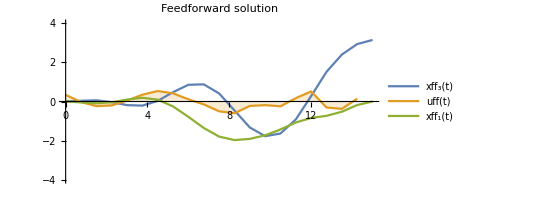
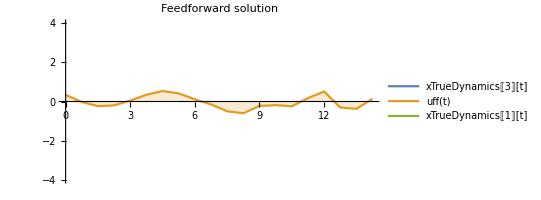
-Graphics- | -Graphics-

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];
ffGeneral[n_,nDim_,x_,λ_,fx_,τ_,τ1_,L_,bcs_]:=Module[{f,Δt,eqns,sv,froot,xff0 = Table[Subscript[xff0, i],{i,1,nDim}],xff = Table[Subscript[xff, i],{i,1,nDim}],uff0,uff},Δt=τ/n;
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0.00001},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,Subscript[xff0, i] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 
For[i = 1,i<=nDim,i++,Subscript[xff, i][t_]:=Piecewise[{{Subscript[xff0, i][t],0≤t≤τ}},Subscript[xff0, i][τ]]]; (* Not fixed Bug here*)
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{xff0,uff}] (* Not fixed Bug here*)

TestGeneral[nDim_,x_,fx_,τ1_,uff_,init_]:=Module[{eq,x1,x2,θ1,θ2,x1s,x2s,θ1s,θ2s,t,replacement},
eq = Table[x[[i]]'[t] == (fx[[i]]/.Join[Table[x[[i]] -> x[[i]][t],{i,1,nDim}],{u -> uff[t]}]),{i,1,nDim}];
xTrueDynamics=NDSolveValue[{eq,init},x,{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
xTrueDynamics]


n=20;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 4;
Δt=τ/n;
x = {x1,x2,θ1,θ2};
λ = {λ1,λ2,λ3,λ4};
Ldynamics = 1/2 *(M+m)*x2^2 + 1/2 *m*l^2*θ2^2 + m*l*Cos[θ1]*x2*θ2 + m*g*l*Cos[θ1] - u*x1; (* Note: u is a scaled version of the original control by a factor of 1/(M+m)*)
fdot[s_] := D[s,x1]*x2 + D[s,x2]*x2dot + D[s,θ1]*θ2 + D[s,θ2]*θ2dot;
eqn1 = fdot[D[Ldynamics,x2]] - D[Ldynamics,x1];
eqn2 = fdot[D[Ldynamics,θ2]] - D[Ldynamics,θ1];
sol = Solve[{eqn1==0,eqn2 == 0},{x2dot,θ2dot}][[1]];
{x2dot,θ2dot} = {x2dot,θ2dot}/.sol ;
fx = {x2,x2dot,θ2,θ2dot};
L = 1/2*u^2; (*Cost function*)
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x1, n]==Subscript[x2, n]==Subscript[θ1, 0]==Subscript[θ2, 0]==Subscript[θ2, n]==0,Subscript[θ1, n]==π};
init = {x1[0] == x2[0] == θ1[0] == θ2[0] == 0};

{xff,uff} = ffGeneral[n,nDim,x,λ,fx,τ,τ1,L,bcs];
xTrueDynamics = TestGeneral[nDim,x,fx,τ,uff,init];

pFeedforward=Plot[{Subscript[xff, 3][t],uff[t],Subscript[xff, 1][t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}];

pTrueDynamics=Plot[{xTrueDynamics[[3]][t],uff[t],xTrueDynamics[[1]][t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}];

Grid[{{pFeedforward,pTrueDynamics}}]
```

Rough Work

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];
ffGeneral[n_,nDim_,x_,λ_,fx_,τ_,τ1_,L_,bcs_]:=Module[{f,Δt,eqns,sv,froot,xff0 = Table[Subscript[xff0, i],{i,1,nDim}],xff = Table[Subscript[xff, i],{i,1,nDim}],uff0,uff},Δt=τ/n;
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0.00001},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,Subscript[xff0, i] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 
For[i = 1,i<=nDim,i++,Subscript[xff, i][t_]:=Piecewise[{{Subscript[xff0, i][t],0≤t≤τ}},Subscript[xff0, i][τ]]]; (* Not fixed Bug here*)
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{xff0,uff}] (* Not fixed Bug here*)
Clear[u];
n=20;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 4;
Δt=τ/n;
x = {x1,x2,θ1,θ2};
λ = {λ1,λ2,λ3,λ4};
Ldynamics = 1/2 *(M+m)*x2^2 + 1/2 *m*l^2*θ2^2 + m*l*Cos[θ1]*x2*θ2 + m*g*l*Cos[θ1] - u*x1; (* Note: u is a scaled version of the original control by a factor of 1/(M+m)*)
fdot[s_] := D[s,x1]*x2 + D[s,x2]*x2dot + D[s,θ1]*θ2 + D[s,θ2]*θ2dot;
eqn1 = fdot[D[Ldynamics,x2]] - D[Ldynamics,x1];
eqn2 = fdot[D[Ldynamics,θ2]] - D[Ldynamics,θ1];
sol = Solve[{eqn1==0,eqn2 == 0},{x2dot,θ2dot}][[1]];
{x2dot,θ2dot} = {x2dot,θ2dot}/.sol ;
fx = {x2,x2dot,θ2,θ2dot};
L = 1/2*u^2; (*Cost function*)
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x1, n]==Subscript[x2, n]==Subscript[θ1, 0]==Subscript[θ2, 0]==Subscript[θ2, n]==0,Subscript[θ1, n]==π};
init = {x1[0] == x2[0] == θ1[0] == θ2[0] == 0};

{xff,uff} = ffGeneral[n,nDim,x,λ,fx,τ,τ1,L,bcs];
fx = {x2,x2dot,θ2,θ2dot};
eq = Table[x[[i]]'[t] == (fx[[i]]/.Join[Table[x[[i]] -> x[[i]][t],{i,1,nDim}],{u -> (uff[t])}]),{i,1,nDim}];
xTrueDynamics=NDSolveValue[{eq,init},x,{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolveValue::dvnoarg: The function θ1 appears with no arguments.

```mathematica
fx[[2]]
```

-(1. (0.-10. (-(10. λ2)/(-11.+1. Cos[θ1]^2)+(10. λ4 Cos[θ1])/(-11.+1. Cos[θ1]^2))+1. θ2^2 Sin[θ1]+1. Cos[θ1] Sin[θ1]))/(-11.+1. Cos[θ1]^2)

```mathematica
init
```

{x1[0]==x2[0]==θ1[0]==θ2[0]==0}

Testing on a Simple System

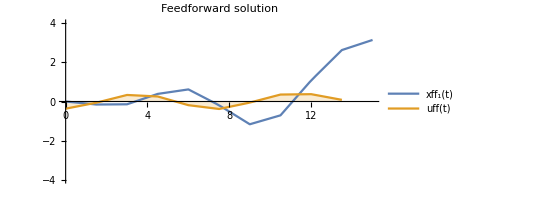

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];
ffGeneral[n_,nDim_,x_,λ_,fx_,τ_,τ1_,L_,bcs_]:=Module[{f,Δt,eqns,sv,froot,xff0 = Table[Subscript[xff0, i],{i,1,nDim}],xff = Table[Subscript[xff, i],{i,1,nDim}],uff0,uff},Δt=τ/n;
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0.00001},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,Subscript[xff0, i] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 

For[i = 1,i<=nDim,i++,Subscript[xff, i][t_]:=Piecewise[{{Subscript[xff0, i][t],0≤t≤τ}},Subscript[xff0, i][τ]]]; (* Not fixed Bug here*)
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
 

{xff0,uff}] (* Not fixed Bug here*)
n=10;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 2;
Δt=τ/n;
x = {x1,x2};
λ = {λ1,λ2};
fx = {x2,-Sin[x1] + u};
L = 1/2*u^2; (*Cost function*)
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x2, n]==0,Subscript[x1, n]==π};
{xff,uff} = ffGeneral[n,nDim,x,λ,fx,τ,τ1,L,bcs];

p1a=Plot[{Subscript[xff, 1][t],uff[t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}]
```

Rough Work

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];

n=2;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 4;
Δt=τ/n;
x = {x1,x2,θ1,θ2};
λ = {λ1,λ2,λ3,λ4};
Ldynamics = 1/2 *(M+m)*x2^2 + 1/2 *m*l^2*θ2^2 + m*l*Cos[θ1]*x2*θ2 + m*g*l*Cos[θ1] - u*x1; (* Note: u is a scaled version of the original control by a factor of 1/(M+m)*)
fdot[s_] := D[s,x1]*x2 + D[s,x2]*x2dot + D[s,θ1]*θ2 + D[s,θ2]*θ2dot;
eqn1 = fdot[D[Ldynamics,x2]] - D[Ldynamics,x1];
eqn2 = fdot[D[Ldynamics,θ2]] - D[Ldynamics,θ1];
sol = Solve[{eqn1==0,eqn2 == 0},{x2dot,θ2dot}][[1]];
{x2dot,θ2dot} = {x2dot,θ2dot}/.sol ;
fx = {x2,x2dot,θ2,θ2dot};
L = 1/2*u^2; (*Cost function*)
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x1, n]==Subscript[x2, n]==Subscript[θ1, 0]==Subscript[θ2, 0]==Subscript[θ2, n]==0,Subscript[θ1, n]==π};eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x1_0,x2_0,θ1_0,θ2_0,λ1_0,λ2_0,λ3_0,λ4_0,x1_1,x2_1,«14»} = {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«14»}. Try perturbing the initial point(s).

```mathematica
eqns
```

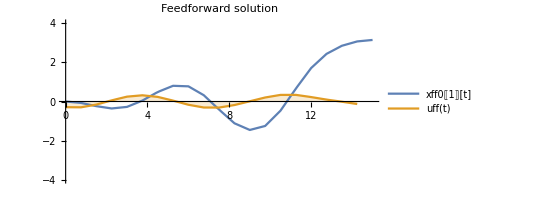

```mathematica
p1a=Plot[{xff0[[1]][t],uff[t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}]
```

General True Dynamics Test function Testing

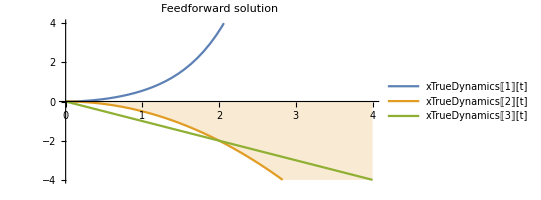

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
TestGeneral[nDim_,x_,fx_,τ1_,uff_,init_]:=Module[{eq,x1,x2,θ1,θ2,x1s,x2s,θ1s,θ2s,t,replacement},
eq = Table[x[[i]]'[t] == (fx[[i]]/.Join[Table[x[[i]] -> x[[i]][t],{i,1,nDim}],{u -> uff[t]}]),{i,1,nDim}];
xTrueDynamics=NDSolveValue[{eq,init},x,{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
xTrueDynamics]

x = {x1,x2,x3};
fx = {x2^2 + x3*u,x3,u};
nDim = 3;
uff[t_] := -1;
init = {x1[0] == x2[0] == x3[0] == 0};
τ1 = 4;
xTrueDynamics = TestGeneral[nDim,x,fx,τ1,uff,init];
p1a=Plot[{xTrueDynamics[[1]][t],xTrueDynamics[[2]][t],xTrueDynamics[[3]][t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}]
```

```mathematica
tempfile=FilenameJoin[{$TemporaryDirectory,"saved.wl"}];
Save[tempfile,S];
```

```mathematica
tempfile=FilenameJoin[{$TemporaryDirectory,"saved.wl"}];
Get[tempfile]; 
S[[1,1]]/.{zero -> 0.00001} (* The original expression had no solution*)
```